```mathematica
Test quadratic and 4th order anharmonic perturbation fit for 4.801Ang Einstein oscillator 2 mode book
;
```

38.408 and Ang anharmonic book Einstein fit for mode order oscillator perturbation quadratic Test th

```mathematica
K2meV=1000*8.617332478*10^−5;
```

```mathematica
(*********4.685Angstrom potentials*******)

(*2nd order fit*)
c2ndPertub4685[x_]:=0.9955521357614084+0.0018894263800479031 x-2.7742223514395397*10^-6 x^2;
z2ndPertub4685[x_]:=0.9959323804637327+0.0005180362904998462*x-1.0433164929822815*(10^-7)*x^2;
(*4th order fit*)
c4thPertub4685[x_]:=0.9956918914010281+0.0018520578078129234 x-4.2900457344043634*(10^-7) x^2-5.138635421885797*(10^-8) x^3+3.632080602609196*(10^-10) x^4
z4thPertub4685[x_]:=0.996018011640013+0.0004999125207652784 x+8.251159873028546*(10^-7) x^2-1.7089559647328497*(10^-8)x^3+1.0342989117824144*(10^-10) x^4

(********4.801Angstrom potentials*******)

(*2nd order fit*)
c2ndPertub4801[x_]:=0.9890058804565284+0.0021458064501972533 x-3.283357864976186*(10^-6)x^2;

z2ndPertub4801[x_]:=0.9988370794773582+0.0006246285950256142 x-8.961226872689955*(10^-8) x^2;
(*4th order fit*)
c4thPertub4801[x_]:=0.9891243138341942+0.0021105586075099696 x-9.152047010130231*(10^-7) x^2-5.434632692492505*(10^-8) x^3+3.971549021931651*(10^-10) x^4;

z4thPertub4801[x_]:=0.9989531107374274+0.0006005640856135567 x+1.1173323636892234*(10^-6) x^2-2.1668278454361286*(10^-8) x^3+1.2783437569792334*(10^-10) x^4;


(*spectrumAnharmonicZtest9= Table[((0.5+x)*(zPertub4801[x])),{x,0,360}];
spectrumAnharmonicCtest9=Table[((0.5+x)*(cPertub4801[x])),{x,0,360}];
spectrumAnharmonicZtest10= Table[((0.5+x)*(z4thPertub4801[x])),{x,0,360}];
spectrumAnharmonicCtest10=Table[((0.5+x)*(c4thPertub4801[x])),{x,0,360}];*)

(*Note - the first set of omega0s is for 4.685Angstrom ZrC and the second is for 4.801Ang*)

cOmega0={31.58754341976066,,,28.84864245230039, };
zOmega0={13.44788050977517,,,11.896801386503334, };



(*************OLD***********
ZanharmonicFit[T_,spectrumZ_,spectrumC_,volIndex_]:={Total[Exp[-2*zOmega0[[volIndex]]*spectrumZ/(K2meV*T)]],Total[Exp[-2*cOmega0[[volIndex]]*spectrumC/(K2meV*T)]]}

free2nd[T_,maxEigen_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T, Table[((0.5+x)*(z2ndPertub4801[x])),{x,0,maxEigen}],Table[((0.5+x)*(c2ndPertub4801[x])),{x,0,maxEigen}]]]

free4th[T_,maxEigen_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,Table[((0.5+x)*(z4thPertub4801[x])),{x,0,maxEigen}],Table[((0.5+x)*(c4thPertub4801[x])),{x,0,maxEigen}]]]



*)

free[T_,spectrumZ_,spectrumC_,maxEigen_,volIndex_]:=-K2meV*1.5*T*Log[{Total[Exp[-2*zOmega0[[volIndex]]*Table[((0.5+x)*(spectrumZ[x])),{x,0,maxEigen}]/(K2meV*T)]],Total[Exp[-2*cOmega0[[volIndex]]*Table[((0.5+x)*(spectrumC[x])),{x,0,maxEigen}]/(K2meV*T)]]}]
free1[T_,spectrumZ_,spectrumC_,maxEigen_,volIndex_]:=-K2meV*1.5*T*Log[{Total[Exp[-2*zOmega0[[volIndex]]*Table[((0.5+x)*(spectrumZ)),{x,0,maxEigen}]/(K2meV*T)]],Total[Exp[-2*cOmega0[[volIndex]]*Table[((0.5+x)*(spectrumC)),{x,0,maxEigen}]/(K2meV*T)]]}]
```

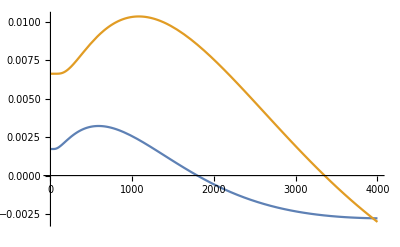

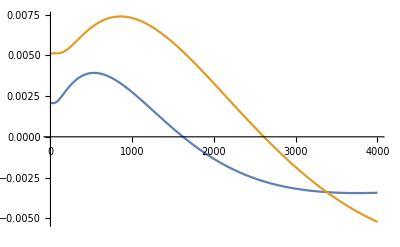

```mathematica
(*4th-2nd order fit difference for 4.685Angstrom*)
Plot[{Evaluate@(free[T,z4thPertub4685,c4thPertub4685,70,1]-(free[T,z2ndPertub4685,c2ndPertub4685,70,1]))
},{T,1,4000}]
(*4th-2nd order fit difference for 4.801Angstrom*)
Plot[{Evaluate@(free[T,z4thPertub4801,c4thPertub4801,70,4]-(free[T,z2ndPertub4801,c2ndPertub4801,70,4]))
},{T,1,4000}]
```

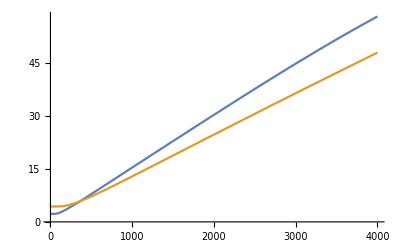

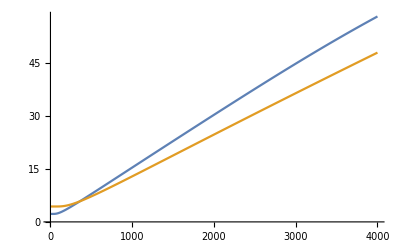

```mathematica
(*2nd order 4.685-4.801-Angstrom difference*)
Plot[{Evaluate@(free[T,z2ndPertub4685,c2ndPertub4685,70,1]-(free[T,z2ndPertub4801,c2ndPertub4801,70,4]))
},{T,1,4000}]
(*4th order 4.685-4.801-Angstrom difference*)
Plot[{Evaluate@(free[T,z4thPertub4685,c4thPertub4685,70,1]-(free[T,z4thPertub4801,c4thPertub4801,70,4]))
},{T,1,4000}]
```

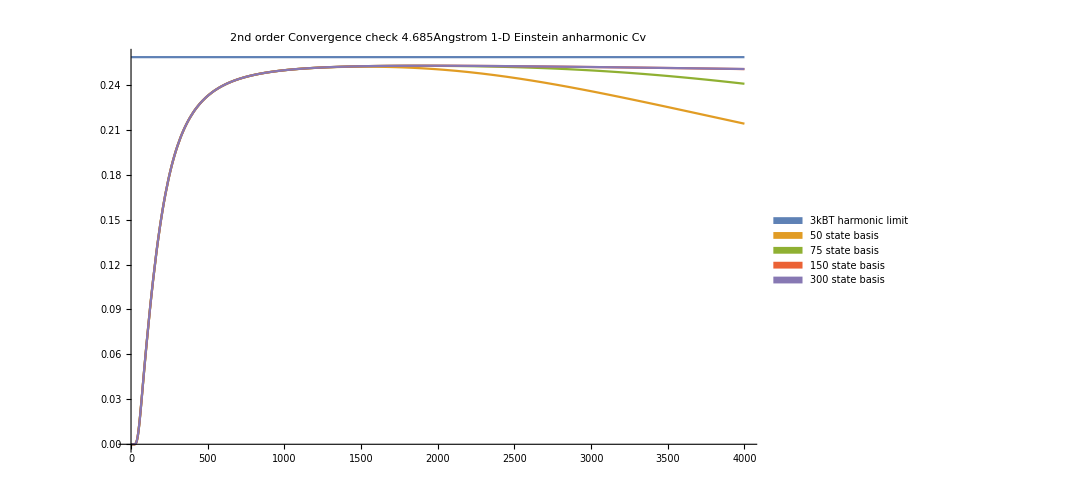

```mathematica
(*Plot ZrC 1D Einstein Heat capcity - 2nd order*)
Plot[{K2meV*3,Total[T*D[-D[free[T,z2ndPertub4685,c2ndPertub4685,50,1],T],T]]/.T->t,Total[T*D[-D[free[T,z2ndPertub4685,c2ndPertub4685,75,1],T],T]]/.T->t,Total[T*D[-D[free[T,z2ndPertub4685,c2ndPertub4685,150,1],T],T]]/.T->t,Total[T*D[-D[free[T,z2ndPertub4685,c2ndPertub4685,300,1],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800,PlotLabel->"2nd order Convergence check 4.685Angstrom 1-D Einstein anharmonic Cv",PlotLegends->SwatchLegend[{"3kBT harmonic limit","50 state basis","75 state basis","150 state basis","300 state basis"}]]
```

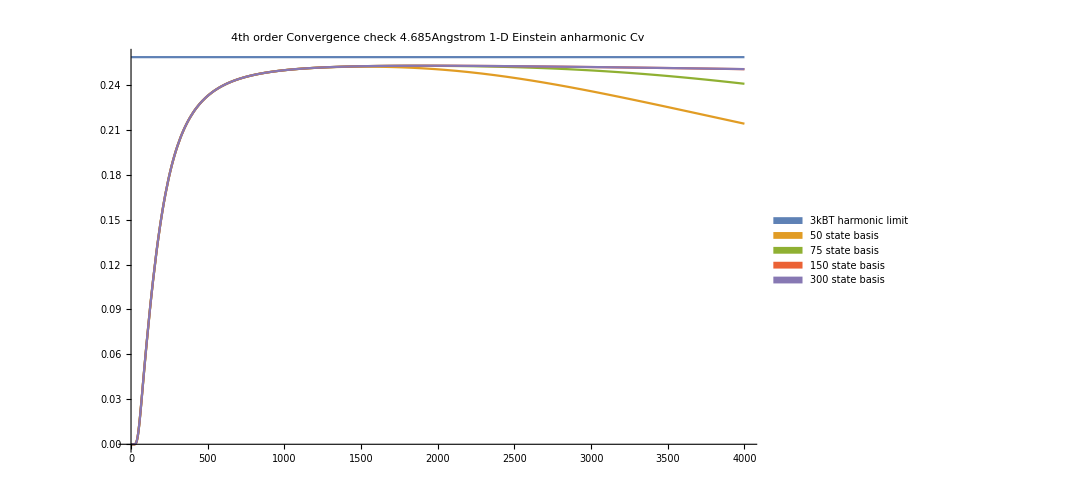

```mathematica
(*Plot ZrC 1D Einstein Heat capcity - 4th order*)
Plot[{K2meV*3,Total[T*D[-D[free[T,z4thPertub4685,c4thPertub4685,50,1],T],T]]/.T->t,Total[T*D[-D[free[T,z4thPertub4685,c4thPertub4685,75,1],T],T]]/.T->t,Total[T*D[-D[free[T,z4thPertub4685,c4thPertub4685,150,1],T],T]]/.T->t,Total[T*D[-D[free[T,z4thPertub4685,c4thPertub4685,300,1],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800,PlotLabel->"4th order Convergence check 4.685Angstrom 1-D Einstein anharmonic Cv",PlotLegends->SwatchLegend[{"3kBT harmonic limit","50 state basis","75 state basis","150 state basis","300 state basis"}]]
```

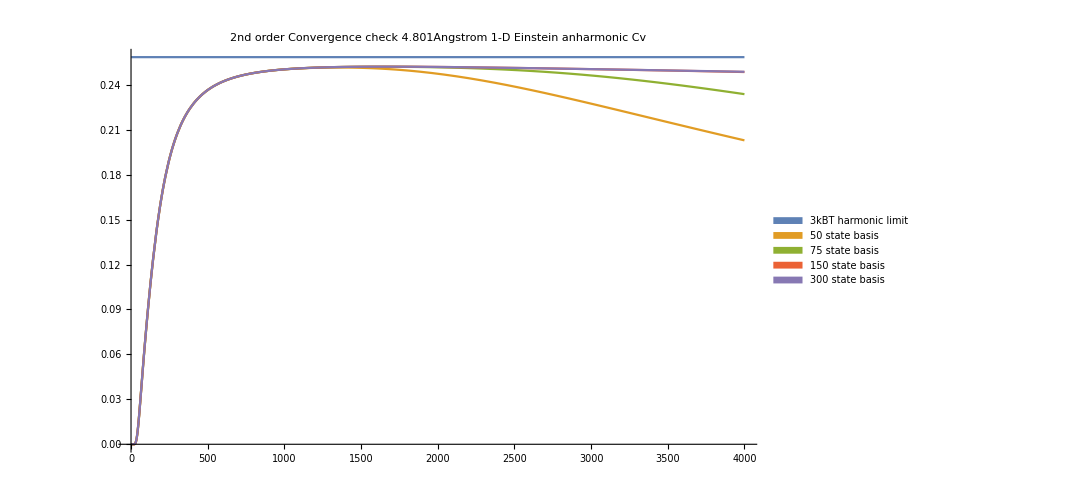

```mathematica
(*Plot ZrC 1D Einstein Heat capcity - 4.801Angstrom -  2nd order*)
Plot[{K2meV*3,Total[T*D[-D[free[T,z2ndPertub4801,c2ndPertub4801,50,4],T],T]]/.T->t,Total[T*D[-D[free[T,z2ndPertub4801,c2ndPertub4801,75,4],T],T]]/.T->t,Total[T*D[-D[free[T,z2ndPertub4801,c2ndPertub4801,150,4],T],T]]/.T->t,Total[T*D[-D[free[T,z2ndPertub4801,c2ndPertub4801,300,4],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800,PlotLabel->"2nd order Convergence check 4.801Angstrom 1-D Einstein anharmonic Cv",PlotLegends->SwatchLegend[{"3kBT harmonic limit","50 state basis","75 state basis","150 state basis","300 state basis"}]]
```

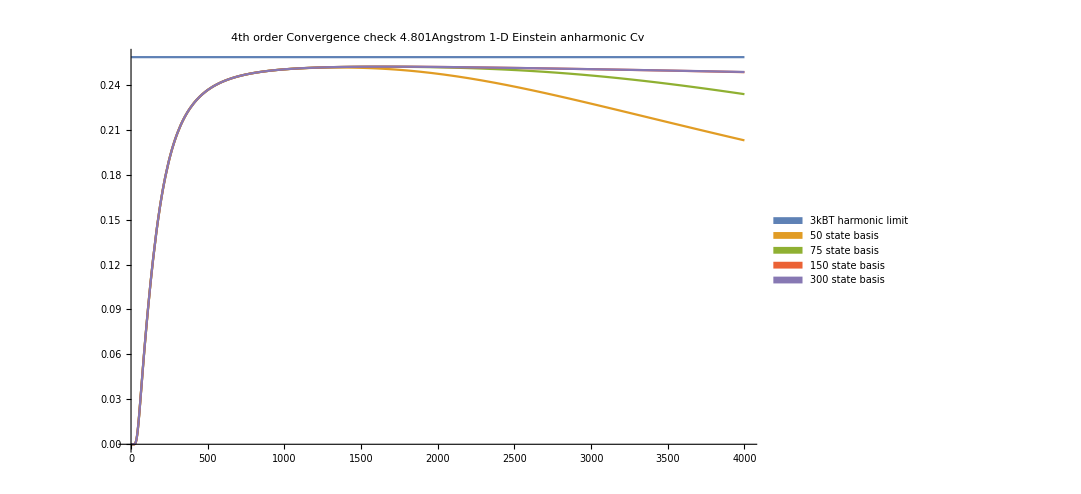

```mathematica
(*Plot ZrC 1D Einstein Heat capcity - 4.801Angstrom -  4th order*)
Plot[{K2meV*3,Total[T*D[-D[free[T,z4thPertub4801,c4thPertub4801,50,4],T],T]]/.T->t,Total[T*D[-D[free[T,z4thPertub4801,c4thPertub4801,75,4],T],T]]/.T->t,Total[T*D[-D[free[T,z4thPertub4801,c4thPertub4801,150,4],T],T]]/.T->t,Total[T*D[-D[free[T,z4thPertub4801,c4thPertub4801,300,4],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800,PlotLabel->"4th order Convergence check 4.801Angstrom 1-D Einstein anharmonic Cv",PlotLegends->SwatchLegend[{"3kBT harmonic limit","50 state basis","75 state basis","150 state basis","300 state basis"}]]
```

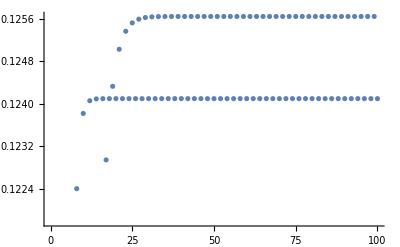

```mathematica
(*Check convergence of heat capcity*)
ListPlot[Flatten@Table[(T*D[-D[free[T,z4thPertub4801,c4thPertub4801,10*i,1],T],T])/.T->3800,{i,1,50}]]
```

```mathematica
(*Plot difference in heat capcity for 4.801 and 4.685 for 4th order fit with 150 eigenvalues*)
```

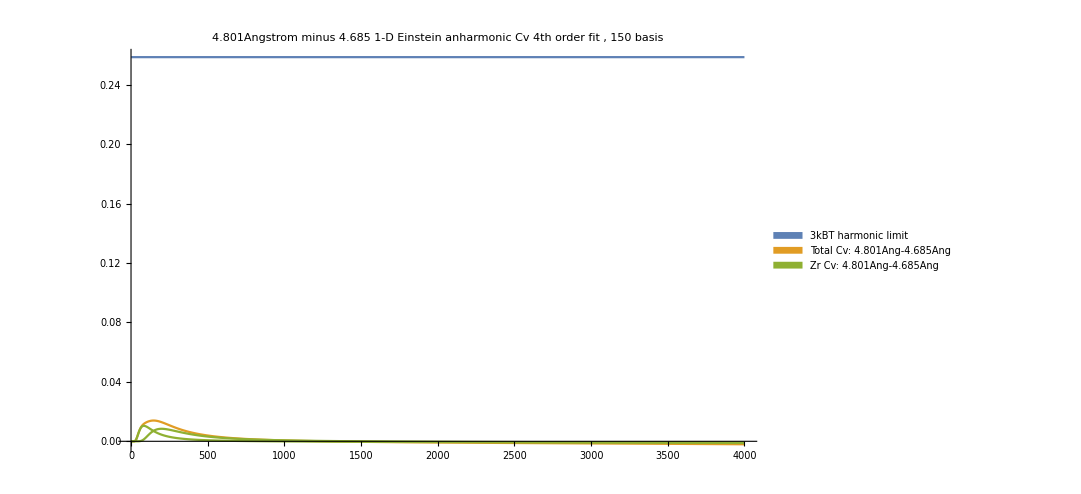

```mathematica
Plot[{K2meV*3,(Total[T*D[-D[free[T,z4thPertub4801,c4thPertub4801,150,4],T],T]]-Total[T*D[-D[free[T,z4thPertub4685,c4thPertub4685,150,1],T],T]])/.T->t,Evaluate@(T*D[-D[free[T,z4thPertub4801,c4thPertub4801,150,4],T],T]-T*D[-D[free[T,z4thPertub4685,c4thPertub4685,150,1],T],T])/.T->t},{t,1,4000},PlotRange->All,ImageSize->800,PlotLabel->"4.801Angstrom minus 4.685 1-D Einstein anharmonic Cv \n 4th order fit , 150 basis",PlotLegends->SwatchLegend[{"3kBT harmonic limit","Total Cv: 4.801Ang-4.685Ang","Zr Cv: 4.801Ang-4.685Ang","C Cv: 4.801Ang-4.685Ang"}]]
```

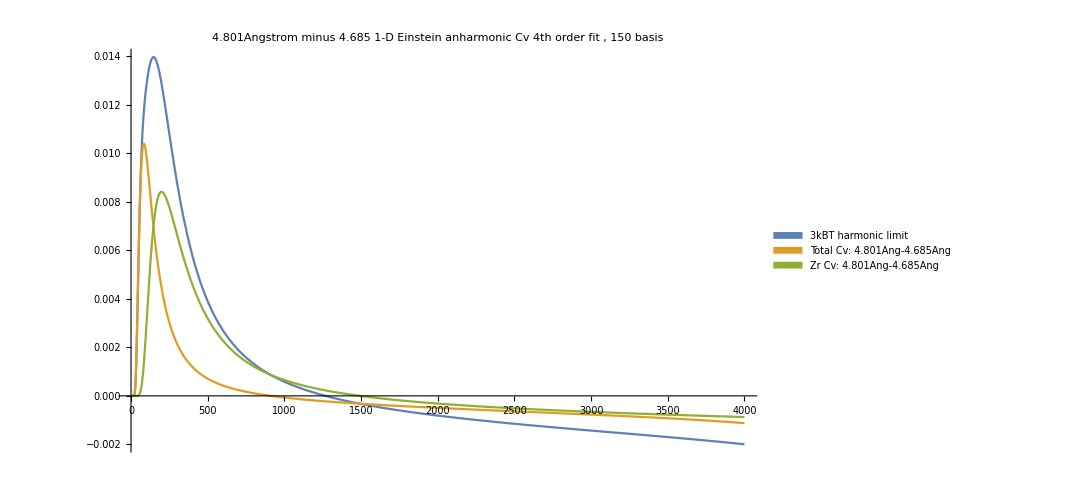

```mathematica
Plot[{(Total[T*D[-D[free[T,z4thPertub4801,c4thPertub4801,150,4],T],T]]-Total[T*D[-D[free[T,z4thPertub4685,c4thPertub4685,150,1],T],T]])/.T->t,Evaluate@Partition[Flatten@(T*D[-D[free[T,z4thPertub4801,c4thPertub4801,150,4],T],T]-T*D[-D[free[T,z4thPertub4685,c4thPertub4685,150,1],T],T])/.T->t,2]},{t,1,4000},PlotRange->All,ImageSize->800,PlotLabel->"4.801Angstrom minus 4.685 1-D Einstein anharmonic Cv \n 4th order fit , 150 basis",PlotLegends->SwatchLegend[{"3kBT harmonic limit","Total Cv: 4.801Ang-4.685Ang","Zr Cv: 4.801Ang-4.685Ang","C Cv: 4.801Ang-4.685Ang"}]]
```

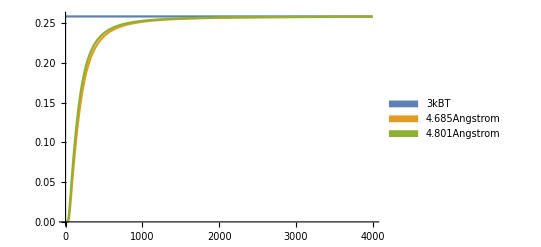

```mathematica
(*Harmonic heat capcity for 4.801 and 4.685Angstrom*)
Plot[{K2meV*3,(Total[T*D[-D[free1[T,1,1,250,1],T],T]])/.T->t,(Total[T*D[-D[free1[T,1,1,250,4],T],T]])/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"3kBT","4.685Angstrom","4.801Angstrom"}],PlotRange->All]
```

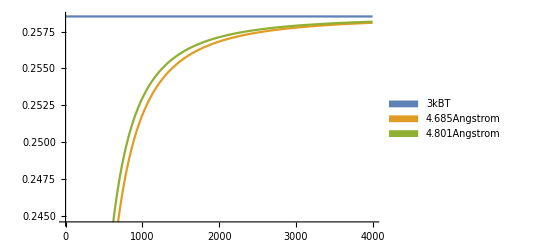

```mathematica
Plot[{K2meV*3,(Total[T*D[-D[free1[T,1,1,250,1],T],T]])/.T->t,(Total[T*D[-D[free1[T,1,1,250,4],T],T]])/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"3kBT","4.685Angstrom","4.801Angstrom"}]]
```

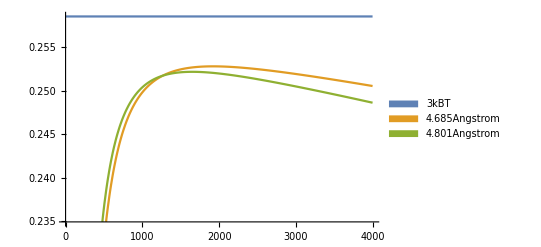

```mathematica
Plot[{K2meV*3,(Total[T*D[-D[free[T,z4thPertub4685,c4thPertub4685,250,1],T],T]])/.T->t,(Total[T*D[-D[free[T,z4thPertub4801,c4thPertub4801,250,4],T],T]])/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"3kBT","4.685Angstrom","4.801Angstrom"}]]
```

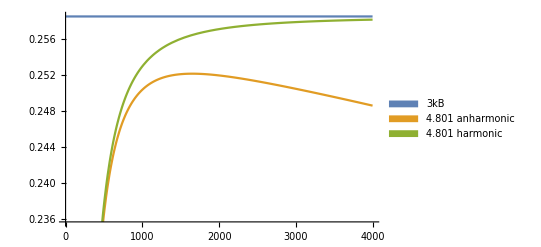

```mathematica
(*4.801Angstrom anharmonic harmonic heat capcity comparison*)
Plot[{K2meV*3,(Total[T*D[-D[free[T,z4thPertub4801,c4thPertub4801,250,4],T],T]])/.T->t,(Total[T*D[-D[free1[T,1,1,250,4],T],T]])/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"3kB","4.801 anharmonic","4.801 harmonic"}]]
```

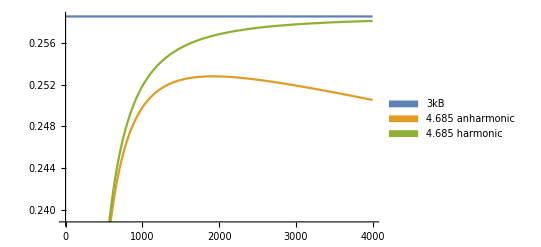

```mathematica
(*4.685Angstrom anharmonic harmonic heat capacity comparison*)
Plot[{K2meV*3,(Total[T*D[-D[free[T,z4thPertub4685,c4thPertub4685,250,1],T],T]])/.T->t,(Total[T*D[-D[free1[T,1,1,250,1],T],T]])/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"3kB","4.685 anharmonic","4.685 harmonic"}]]
```

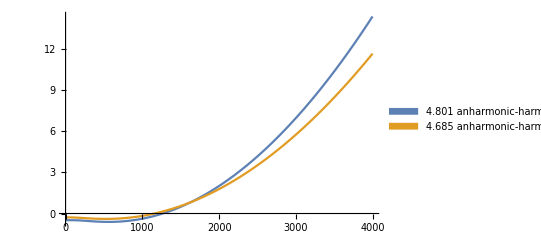

```mathematica
(*4.685Angstrom anharmonic harmonic free energy comparison*)
Plot[{(Total[free[T,z4thPertub4801,c4thPertub4801,250,4]]-Total[free1[T,1,1,250,4]])/.T->t,(Total[free[T,z4thPertub4685,c4thPertub4685,250,1]]-Total[free1[T,1,1,250,1]])/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"4.801 anharmonic-harmonic","4.685 anharmonic-harmonic"}]]
```